```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 154 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[r]
r = { x[t] + s[t] Cos[α]  , h - s[t] Sin[α] }
```

{Cos[α] s[t]+x[t],h-s[t] Sin[α]}

```mathematica
D[r, t]
```

{Cos[α] s'[t]+x'[t],-Sin[α] s'[t]}

```mathematica
D[r, t]
```

{Cos[α] s'[t]+x'[t],-Sin[α] s'[t]}

```mathematica
D[r, t] . D[r, t]
```

Sin[α]^2 s'[t]^2+(Cos[α] s'[t]+x'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand // Simplify
```

s'[t]^2+2 Cos[α] s'[t] x'[t]+x'[t]^2

```mathematica
Clear[T]
T = 1/2 M x'[t]^2 + 1/2 m ( D[r, t] . D[r, t]  // Expand // Simplify  )
```

1/2 M x'[t]^2+1/2 m (s'[t]^2+2 Cos[α] s'[t] x'[t]+x'[t]^2)

```mathematica
r
r[[2]]
```

{Cos[α] s[t]+x[t],h-s[t] Sin[α]}

h-s[t] Sin[α]

```mathematica
Clear[V1]
V1= m g r[[2]]
```

g m (h-s[t] Sin[α])

```mathematica
Clear[V2]
V2 = 1/2 k ( s[t]-d)^2
```

1/2 k (-d+s[t])^2

```mathematica
Clear[V]
V = Union[ V1 , V2 ]
```

1/2 g k m (-d+s[t])^2 (h-s[t] Sin[α])

```mathematica
Clear[ℒ]
ℒ = T - V   ;
ℒ // pdConv
```

-1/2 g k m (s(t)-d)^2 (h-sin(α) s(t))+1/2 m (2 cos(α) (∂s(t))/(∂t) (∂x(t))/(∂t)+((∂s(t))/(∂t))^2+((∂x(t))/(∂t))^2)+1/2 M ((∂x(t))/(∂t))^2

```mathematica
Clear[q]
q = { x[t] , s[t] }
```

{x[t],s[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ] == 0 
D[ D[ ℒ , D[q[[2]], t] ], t ]  - D[ ℒ , q[[2]] ] == 0
```

M x''[t]+1/2 m (2 Cos[α] s''[t]+2 x''[t])==0

-1/2 g k m (-d+s[t])^2 Sin[α]+g k m (-d+s[t]) (h-s[t] Sin[α])+1/2 m (2 s''[t]+2 Cos[α] x''[t])==0

```mathematica
Table[ 
D[ D[ ℒ , D[q[[i]], t] ], t ]  - D[ ℒ , q[[i]] ]== 0  , 
{ i, 1, 2 } ] //Expand // Simplify //  TableForm
(* This looks wrong *)
```

m Cos[α] s''[t]+(m+M) x''[t]==0
m (2 d g h k+d^2 g k Sin[α]+3 g k s[t]^2 Sin[α]-2 g k s[t] (h+2 d Sin[α])-2 s''[t]-2 Cos[α] x''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-m Cos[α] s''[t]-(m+M) x''[t]==0
1/2 m (g k (d-s[t])^2 Sin[α]-2 g k (-d+s[t]) (h-s[t] Sin[α])-2 s''[t]-2 Cos[α] x''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m -> 2 , 
M-> 20 , 
g-> 9.8 , 
h -> 0.5 , 
α -> π/12 ,
k-> 50 ,
d->  0.3 
} ;
parameters // TableForm
```

m→2
M→20
g→9.8
h→0.5
α→π/12
k→50
d→0.3

```mathematica
eqs /. parameters // TableForm
```

-((1+√3) s''[t])/(√2)-22 x''[t]==0
126.821 (0.3-s[t])^2-980. (-0.3+s[t]) (0.5-((-1+√3) s[t])/(2 √2))-2 s''[t]-((1+√3) x''[t])/(√2)==0

```mathematica
Clear[ics]
ics = {
s[0] == 0.4 , 
s'[0] == 0.5 , 
x[0] == 0 , 
x'[0] == 0 
} ;
ics // TableForm
```

s[0]==0.4
s'[0]==0.5
x[0]==0
x'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q, { t, 0, 100 } ]]
```

{x[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

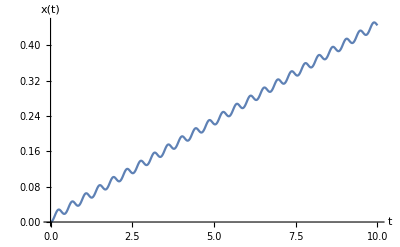

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 10 }, AxesLabel-> { t , q[[1]] }  ]
```

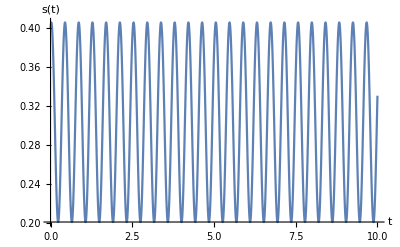

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t , q[[2]] }]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.01 , 20 , 0.5  } ]
```